Swap takes in a list as the first argument and a pair of indices as the second argument. It swaps the two values in the list at the indices.

```mathematica
Swap[state_,pair_]:=
Module[{newState},newState = state;
newState[[pair]] = newState[[Reverse[pair]]];
newState];
```

A simple example.

```mathematica
state = {0,0,1,1,0};
Swap[state,{3,2}]
```

{0,1,0,1,0}

noOverlap takes a list of lists and returns true if all sub lists of the given list have no elements in common

```mathematica
noOverlap[pairs_]:=AllTrue[Permutations[pairs,{2}],{}===Intersection@@#&]
```

```mathematica
noOverlap[{{1,2},{3,4},{2,3}}]
```

False

```mathematica
noOverlap[{{1,2,3},{3,4}}]
```

False

Possible swaps generates a list of pairs of integers that are allowed to be swapped for a circle of interaction length 1.

```mathematica
PossibleSwaps[n_]:=Partition[Append[Range[n],1],2,1];
```

```mathematica
PossibleSwaps[5]
```

{{1,2},{2,3},{3,4},{4,5},{5,1}}

```mathematica
allSetsOfSwaps[n_]:=Module[{allSwaps},

(*if E=2 the number of swaps consider doesnt need to be more than 2, in general 2 should be replaced with n*)
allSwaps = Permutations[PossibleSwaps[n],2];

(*remove sets of swaps if any two of the swaps overlap*)
allSwaps = Select[allSwaps,DuplicateFreeQ[Flatten[#]]&];

(*remove duplicate sets of swaps*) 
(*sort is used so that {{1,2}{3,4}} matches with {{3,4},{1,2}}*)
allSwaps = DeleteDuplicates[allSwaps,Sort[#1]==Sort[#2]&]
]
```

```mathematica
allSetsOfSwaps[6]//MatrixForm (*The matrix form is just for easy viewing*)
```

({}
{{1,2}}
{{2,3}}
{{3,4}}
{{4,5}}
{{5,6}}
{{6,1}}
{{1,2},{3,4}}
{{1,2},{4,5}}
{{1,2},{5,6}}
{{2,3},{4,5}}
{{2,3},{5,6}}
{{2,3},{6,1}}
{{3,4},{5,6}}
{{3,4},{6,1}}
{{4,5},{6,1}})

```mathematica
PossibleCorrelation[state_]:=Module[{n,allSwaps,allPossibleCorrelations,tempState},
n = Length[state];
allSwaps = allSetsOfSwaps[n];

(*perform all the swaps*)
allPossibleCorrelations = 
Table[
tempState = state;
Do[
tempState = Swap[tempState,swap],
{swap,swaps}];
tempState,
{swaps,allSwaps}];

(*Remove duplicates*)
DeleteDuplicates[allPossibleCorrelations]

]
```

```mathematica
StateGraph[n_,e_]:=Module[{protoState,allStates,edges},

protoState = Table[If[i<=e,1,0],{i,n}];
allStates = Permutations[protoState];

edges = Table[
state<->correlation
,{state,allStates},
{correlation,PossibleCorrelation[state]}];

SimpleGraph[ Flatten[edges,1]]
]
```

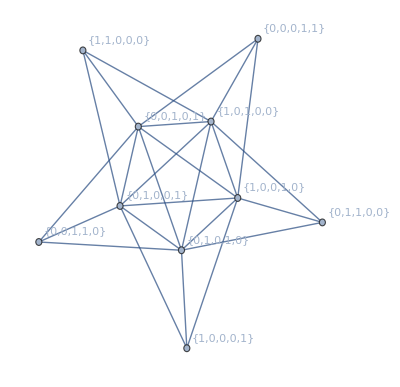

```mathematica
Graph[StateGraph[5,2],VertexLabels-> All]
```

This function give the adjacency matrix for a given number of qbits and energy level. It is different than running AdjacencyMatrix[StateGraph[n,e]] because it enforces canonical ordering.

```mathematica
AdjacencyMatrixInEnergySubspaceforEnergy[n_,e_]:=Module[{protoState,allStates,numStates,edges,stateAdjacencyMatrix,stateNum,correlationNum,numbers},
Assert[n>e];
protoState = Table[If[i<=e,1,0],{i,n}];
allStates = Permutations[protoState];
numStates = Length[allStates];
stateAdjacencyMatrix = Table[0,numStates,numStates];
numbers = Sort[Table[FromDigits[state,2],{state,allStates}]];
Do[
stateNum =Position[numbers,FromDigits[state,2]][[1]];
correlationNum = Position[numbers,FromDigits[correlation,2]][[1]];
stateAdjacencyMatrix[[stateNum,correlationNum]] = 1;
,{state,allStates},
{correlation,PossibleCorrelation[state]}];
stateAdjacencyMatrix
]
```

```mathematica
ArrayPlot[AdjacencyMatrixInEnergySubspaceforEnergy[15,2],Mesh->"Nonzero"](*in canonical ordering within the energy subspace*)
```

-Graphics-

```mathematica
Table[{n,Counts[Total[AdjacencyMatrixInEnergySubspaceforEnergy[n,2]]]},{n,2,17}]//MatrixForm(*in canonical ordering within the energy subspace*)
```

(2 | <|1→1|>
3 | <|3→3|>
4 | <|4→4,6→2|>
5 | <|4→5,8→5|>
6 | <|4→6,8→6,9→3|>
7 | <|4→7,8→7,9→7|>
8 | <|4→8,8→8,9→12|>
9 | <|4→9,8→9,9→18|>
10 | <|4→10,8→10,9→25|>
11 | <|4→11,8→11,9→33|>
12 | <|4→12,8→12,9→42|>
13 | <|4→13,8→13,9→52|>
14 | <|4→14,8→14,9→63|>
15 | <|4→15,8→15,9→75|>
16 | <|4→16,8→16,9→88|>
17 | <|4→17,8→17,9→102|>)

```mathematica
FullSimplify[4n+8n+ 9 n(n-5)1/2]
```

3/2 n (-7+3 n)

```mathematica
Table[{n,3/2 n (-7+3 n)},{n,6,17}]//MatrixForm
```

(6 | 99
7 | 147
8 | 204
9 | 270
10 | 345
11 | 429
12 | 522
13 | 624
14 | 735
15 | 855
16 | 984
17 | 1122)

```mathematica
(*in whatever order states happen to be generated*)
ArrayPlot[AdjacencyMatrix[StateGraph[20,2]]]
```

-Graphics-

```mathematica
AdjacencyMatrixforEnergy[n_,e_]:=Module[{protoState,allStates,numStates,edges,stateAdjacencyMatrix,stateNum,correlationNum,numbers},
Assert[n>e];
protoState = Table[If[i<=e,1,0],{i,n}];
allStates = Permutations[protoState];
numStates = Length[allStates];
stateAdjacencyMatrix = Table[0,2^n,2^n];
Do[
stateNum =FromDigits[state,2];
correlationNum = FromDigits[correlation,2];
stateAdjacencyMatrix[[stateNum,correlationNum]] = 1;
,{state,allStates},
{correlation,PossibleCorrelation[state]}];
stateAdjacencyMatrix
]
```

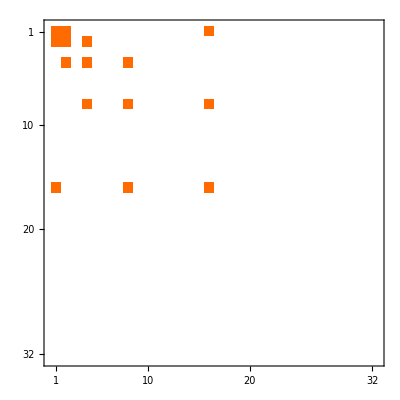

```mathematica
MatrixPlot[AdjacencyMatrixforEnergy[5,1]]
```

```mathematica
FullAdjacencyMatrixCanonical[n_]:=Module[{protoState,allStates,numStates,edges,stateAdjacencyMatrix,stateNum,correlationNum,numbers},


stateAdjacencyMatrix = Table[0,2^n,2^n];
Do[
protoState = Table[If[i<=e,1,0],{i,n}];
allStates = Permutations[protoState];
numStates = Length[allStates];
Do[
stateNum =FromDigits[state,2];
correlationNum = FromDigits[correlation,2];
stateAdjacencyMatrix[[stateNum,correlationNum]] = 1;
,{state,allStates},
{correlation,PossibleCorrelation[state]}];
,{e,n}];
stateAdjacencyMatrix
]
```

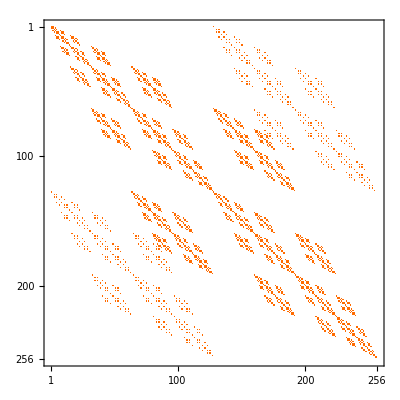

```mathematica
FullAdjacencyMatrixCanonical[8]//MatrixPlot
```

```mathematica
FullAdjacencyMatrixEnergyBasis[n_]:=Module[{protoState,allStates,numStates,edges,stateAdjacencyMatrix,stateNum,correlationNum,numbers,index},


stateAdjacencyMatrix = Table[0,2^n,2^n];

allStates = {};
Do[

protoState = Join[Table[0,n-e],Table[1,e]];

allStates = Union[allStates,Permutations[protoState]];
,{e,0,n}];
numStates = Length[allStates];
numbers = Sort[Table[state,{state,allStates}],Total[#1]<Total[#2]&];
numbers = Table[FromDigits[num,2],{num,numbers}];


Do[

stateNum =Position[numbers,FromDigits[state,2]][[1]];
correlationNum =Position[numbers,FromDigits[correlation,2]][[1]];

stateAdjacencyMatrix[[stateNum,correlationNum]] = 1;
,{state,allStates},
{correlation,PossibleCorrelation[state]}];

stateAdjacencyMatrix
]
```

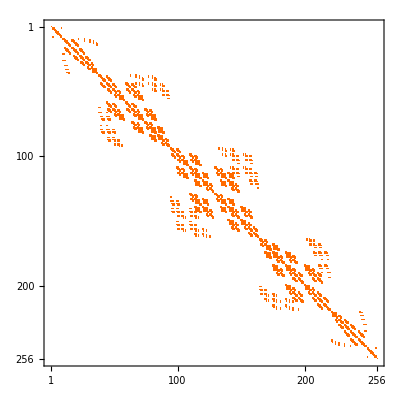

```mathematica
FullAdjacencyMatrixEnergyBasis[8]//MatrixPlot
```